Wolfram Online Mini Campus. Part 17

Instagram Posts
Pinterest Posts
"Translation" of  SageMath Online Mini Campus. Part 17
http://www.wolfram.com/broadcast/video.php?c=460&v=2665

Exercises with PolyhedronData

```mathematica
PolyhedronData["Classes"]
```

{Amphichiral,Antiprism,Archimedean,ArchimedeanDual,Chiral,Compound,Concave,Convex,Deltahedron,Dipyramid,Equilateral,Isohedron,Johnson,KeplerPoinsot,Platonic,PlatonicDual,Prism,Pyramid,Quasiregular,Rhombohedron,Rigid,SelfDual,Shaky,SpaceFilling,Stellation,Uniform,UniformDual,Zonohedron}

Polyhedron Data Classes
{Amphichiral,Antiprism,Archimedean,ArchimedeanDual,Chiral,Compound,Concave,Convex,Deltahedron,Dipyramid,Equilateral,
Isohedron,Johnson,KeplerPoinsot,Platonic,PlatonicDual,Prism,Pyramid,Quasiregular,Rhombohedron,Rigid,SelfDual,Shaky,SpaceFilling,
Stellation,Uniform,UniformDual,Zonohedron}

Archimedean
{Cuboctahedron,GreatRhombicosidodecahedron,GreatRhombicuboctahedron,Icosidodecahedron,SmallRhombicosidodecahedron,SmallRhombicuboctahedron,
SnubCube,SnubDodecahedron,TruncatedCube,TruncatedDodecahedron,TruncatedIcosahedron,TruncatedOctahedron,TruncatedTetrahedron}

ArchimedeanDual
{DeltoidalHexecontahedron,DeltoidalIcositetrahedron,DisdyakisDodecahedron,DisdyakisTriacontahedron,PentagonalHexecontahedron,
PentagonalIcositetrahedron,PentakisDodecahedron,RhombicDodecahedron,RhombicTriacontahedron,SmallTriakisOctahedron,TetrakisHexahedron,
TriakisIcosahedron,TriakisTetrahedron}

Chiral
{GyroelongatedPentagonalBicupola,GyroelongatedPentagonalBirotunda,GyroelongatedPentagonalCupolarotunda,
GyroelongatedSquareBicupola,GyroelongatedTriangularBicupola,
PentagonalHexecontahedron,PentagonalIcositetrahedron,SnubCube,SnubDodecahedron}

Uniform
{Cube,Cuboctahedron,Dodecahedron,GreatDodecahedron,GreatIcosahedron,GreatRhombicosidodecahedron,GreatRhombicuboctahedron,
GreatStellatedDodecahedron,Icosahedron,Icosidodecahedron,Octahedron,SmallRhombicosidodecahedron,SmallRhombicuboctahedron,
SmallStellatedDodecahedron,SnubCube,SnubDodecahedron,Tetrahedron,TruncatedCube,TruncatedDodecahedron,TruncatedIcosahedron,
TruncatedOctahedron,TruncatedTetrahedron}

UniformDual
{Cube,DeltoidalHexecontahedron,DeltoidalIcositetrahedron,DisdyakisDodecahedron,DisdyakisTriacontahedron,Dodecahedron,
GreatDodecahedron,GreatIcosahedron,GreatStellatedDodecahedron,Icosahedron,Octahedron,PentagonalHexecontahedron,
PentagonalIcositetrahedron,PentakisDodecahedron,RhombicDodecahedron,RhombicTriacontahedron,SmallStellatedDodecahedron,
SmallTriakisOctahedron,SmallTriambicIcosahedron,Tetrahedron,TetrakisHexahedron,TriakisIcosahedron,TriakisTetrahedron

```mathematica
AP1=AugmentedPolyhedron[PolyhedronData["SnubDodecahedron","Polyhedron"],4];
AP2=AugmentedPolyhedron[PolyhedronData["PentagonalHexecontahedron","Polyhedron"],3];
Show[ListPlot3D[AP2[[1]],PlotStyle->Opacity[.3],
ColorFunction->"DeepSeaColors",Mesh->All,MeshStyle->Gray],
Graphics3D[{Blue,FaceForm[Opacity[.7],White],EdgeForm[Gray],AP2}],
   Boxed->False,Axes->False,AspectRatio->1,ImageSize->{500,500}]
```

-Graphics3D-

```mathematica
AP=AugmentedPolyhedron[PolyhedronData["Spikey","Polyhedron"],2];
PAP=Table[AP[[1]][[AP[[2,i]]]],{i,Length[AP[[2]]]}];
Show[Graphics3D[Table[Style[Tube[PAP[[i]],.03],Hue[Pi*i/192]],
{i,Length[AP[[2]]]}]],Boxed->False,ImageSize->{500,500}]
```

-Graphics3D-

```mathematica
With [{p="GyroelongatedPentagonalBirotunda"},
Graphics3D[{Tube[PolyhedronData[p,"Edges","Coordinates"],.03],
FaceForm[Opacity[.7],White],
Transpose[{ColorData["Crayola","ColorList"][[11;;10+Length[#]]],#}]},
  Boxed->False]&@PolyhedronData[p,"Polygons"]]
```

-Graphics3D-

Exercises with Surfaces

```mathematica
ColorData["Gradients"]
```

{AlpineColors,Aquamarine,ArmyColors,AtlanticColors,AuroraColors,AvocadoColors,BeachColors,BlueGreenYellow,BrassTones,BrightBands,BrownCyanTones,CandyColors,CherryTones,CMYKColors,CoffeeTones,DarkBands,DarkRainbow,DarkTerrain,DeepSeaColors,FallColors,FruitPunchColors,FuchsiaTones,GrayTones,GrayYellowTones,GreenBrownTerrain,GreenPinkTones,IslandColors,LakeColors,LightTemperatureMap,LightTerrain,MintColors,NeonColors,Pastel,PearlColors,PigeonTones,PlumColors,Rainbow,RedBlueTones,RedGreenSplit,RoseColors,RustTones,SandyTerrain,SiennaTones,SolarColors,SouthwestColors,StarryNightColors,SunsetColors,TemperatureMap,ThermometerColors,ValentineTones,WatermelonColors}

```mathematica
RevolutionPlot3D[{1+u^2/4,1-u^3/8,u},{u,-4,8},{phi,0,2Pi},
ColorFunction->Function[{x,y,z},ColorData["CandyColors"][Cos[169x+144y+121z]]],
PlotRange->{{-5,5},{-5,5},{-5,5}},PlotPoints->200,
MeshStyle->{Gray,LightGray},Axes->False,Boxed->False]
```

-Graphics3D-

Exercises with Functions

```mathematica
fl={-Sin[x],Cos[-x],-Tan[x],Exp[-x]};dfl=Table[D[fl[[i]],x],{i,4}];
Plot[{fl,dfl},{x,-1,1},PlotLegends->"Expressions",
PlotStyle->Table[{Dashing[.006i],Hue[Sin[Pi/8+Pi*i/2]]},{i,8}],
Frame->True,GridLines->Automatic,ImageSize->{500,300}]
```

-Graphics-

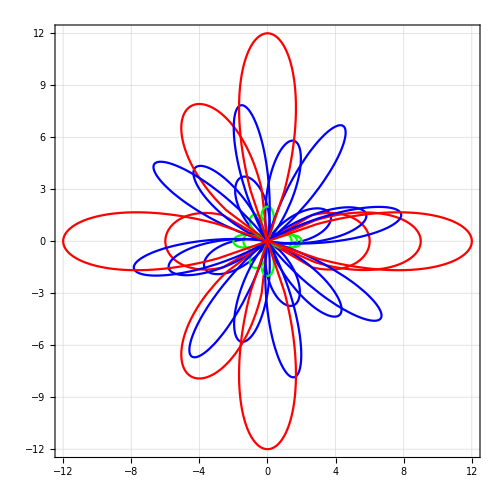

```mathematica
rho[phi_,r_,n_] :=If[ n ==1&&r*Cos[r*phi]≥0,Sqrt[r*Cos[r*phi]],
If[n==2,2r*Cos[r*phi-Pi/4]^2,If[n==3&&3r*Cos[r*phi]≥3,3r*Cos[r*phi],0]]];
Show[Table[PolarPlot[rho[phi,r,i],{phi,0,2Pi},PlotStyle->Hue[i/3]],{r,{2,3,4}},{i,3}],
Frame->True,GridLines->Automatic,PlotRange->All,ImageSize->{500,500}]
```

Exercises with GraphData

```mathematica
With[{l="HighDimensionalEmbedding"},
GraphPlot3D[HighlightGraph[GraphData["HundredTwentyCellGraph","Edges"],
Table[Style[_ <-> i,ColorData["Rainbow"][Pi*i/1800]],{i,Range[1,600,3]}]],
VertexSize->0,GraphLayout->l,ImageSize->Large]]
```

-Graphics3D-

```mathematica
GraphPlot[HighlightGraph[GraphData["HundredTwentyCellGraph"],
Table[Style[_<->i,ColorData["DarkRainbow"][Pi*i/1800]],
{i,Range[1,600,3]}]],VertexSize->0]
```

-Graphics-

```mathematica
GPG[g_,col_]:=GraphPlot[GraphData[g],VertexSize->0,
PlotStyle->RGBColor[col]];
Show[GPG["HundredTwentyCellGraph","slategray"],
         GPG["SixHundredCellGraph","steelblue"]]
```

-Graphics-

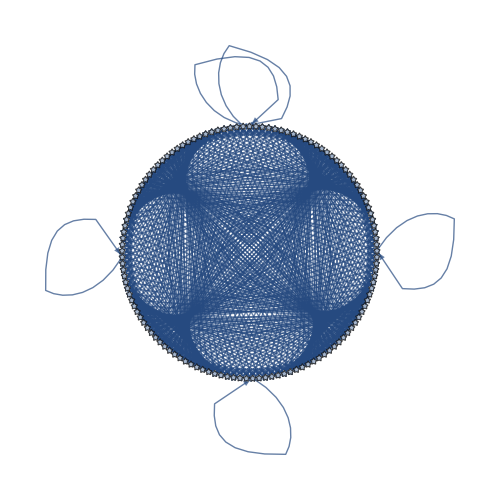

```mathematica
GraphPlot[HighlightGraph[DeBruijnGraph[5,3],
Table[Style[i->j,Hue[i/129]],{j,128},{i,128}]],
    VertexShapeFunction->"ConcavePentagon", ImageSize->{500,500}]
```

Exercises with Datasets

```mathematica
user="https://raw.githubusercontent.com/OlgaBelitskaya/";
path="machine_learning_engineer_nd009/master/Machine_Learning_Engineer_ND_P3/";
data=Import[StringJoin[user,path,"customers.csv"]]; 
Dataset[data[[1;;5]]]
```

```mathematica
TableForm[data[[2;;5]],TableHeadings->{None,data[[1]]}]
```

Channel | Region | Fresh | Milk | Grocery | Frozen | Detergents_Paper | Delicatessen
2 | 3 | 12669 | 9656 | 7561 | 214 | 2674 | 1338
2 | 3 | 7057 | 9810 | 9568 | 1762 | 3293 | 1776
2 | 3 | 6353 | 8808 | 7684 | 2405 | 3516 | 7844
1 | 3 | 13265 | 1196 | 4221 | 6404 | 507 | 1788

```mathematica
TabView[Table[data[[1,i]]->data[[j,i]],{j,Range[2,30,1]},{i,Range[3,8,1]}]]
```

1234567891011121314151617181920212223242526272829

```mathematica
ListLinePlot[Table[data[[All,i]],{i,Range[3,8,1]}],PlotLegends->data[[1,3;;8]],
PlotStyle->Table[ColorData["BrightBands"][i/6],{i,6}],Filling->Axis,
ImageSize->{900,450},AspectRatio->1/2,PlotRange->All,GridLines->All]
```

-Graphics-

Exercises with HTML & CSS Elements

```mathematica
EmbeddedHTML["<style>@import url('https://fonts.googleapis.com/css?family=Ewert');
circle {fill:#3636ff; stroke-width:5; stroke:#fff; transition:transform .7s;}
circle:hover {-ms-transform: scale(1.5); -webkit-transform: scale(1.5); transform: scale(1.5);}
svg {background:silver; width:200px; height:200px;}</style>
<h3 style='color:#3636ff; font-family:Ewert; font-size:140%; 
text-shadow:5px 5px 5px silver;'>Zoom on Hover</h3>
<svg><g transform='translate(100,100)'><circle cx='0' cy='0' r='50'></circle></g></svg>"]
```

Null<style>@import url('https://fonts.go…'0' cy='0' r='50'></circle></g></svg><style>@import url('https://fonts.googleapis.com/css?family=Ewert');
circle {fill:#3636ff; stroke-width:5; stroke:#fff; transition:transform .7s;}
circle:hover {-ms-transform: scale(1.5); -webkit-transform: scale(1.5); transform: scale(1.5);}
svg {background:silver; width:200px; height:200px;}</style>
<h3 style='color:#3636ff; font-family:Ewert; font-size:140%; 
text-shadow:5px 5px 5px silver;'>Zoom on Hover</h3>
<svg><g transform='translate(100,100)'><circle cx='0' cy='0' r='50'></circle></g></svg>

```mathematica
EmbeddedHTML["<div id='test_plotly' style='width:600px; height:400px;'></div>
<script src='//cdn.plot.ly/plotly-latest.min.js'></script><script>
TEST1=document.getElementById('test_plotly');
var x1=Array(80).fill(0.05).map((r,t)=>(r*(t-40)));
var y1=Array(80).fill(0.05).map((r,t)=>(Math.exp(-Math.pow(r*(t-40),2))));
var y2=Array(80).fill(0.05).map((r,t)=>(-Math.exp(-Math.pow(r*(t-40),2))));
var y3=Array(80).fill(0.05).map((r,t)=>(Math.sin(Math.PI*Math.pow(r*(t-40),3))*Math.exp(-Math.pow(r*(t-40),2))));
Plotly.plot(TEST1,[{x:x1,y:y1,line:{color:'#3636ff'},marker:{symbol:317},mode:'markers',
                    hoverinfo:'y',name:'f(x) = e^(-x^2)'}]);
Plotly.plot(TEST1,[{x:x1,y:y2,line:{color:'#36ff36'},marker:{symbol:218},mode:'markers',
                    hoverinfo:'y',name:'f(x) = -e^(-x^2)'}]);
Plotly.plot(TEST1,[{x:x1,y:y3,line:{color:'#ff3636'},mode:'text',text:'☕',
                    hoverinfo:'y',name:'f(x) = sin(πx^3) e^(-x^2)'}]);
</script>",ImageSize->{650,450}]
```

Null«965»<div id='test_plotly' style='width:600px; height:400px;'></div>
<script src='//cdn.plot.ly/plotly-latest.min.js'></script><script>
TEST1=document.getElementById('test_plotly');
var x1=Array(80).fill(0.05).map((r,t)=>(r*(t-40)));
var y1=Array(80).fill(0.05).map((r,t)=>(Math.exp(-Math.pow(r*(t-40),2))));
var y2=Array(80).fill(0.05).map((r,t)=>(-Math.exp(-Math.pow(r*(t-40),2))));
var y3=Array(80).fill(0.05).map((r,t)=>(Math.sin(Math.PI*Math.pow(r*(t-40),3))*Math.exp(-Math.pow(r*(t-40),2))));
Plotly.plot(TEST1,[{x:x1,y:y1,line:{color:'#3636ff'},marker:{symbol:317},mode:'markers',
                    hoverinfo:'y',name:'f(x) = e^(-x^2)'}]);
Plotly.plot(TEST1,[{x:x1,y:y2,line:{color:'#36ff36'},marker:{symbol:218},mode:'markers',
                    hoverinfo:'y',name:'f(x) = -e^(-x^2)'}]);
Plotly.plot(TEST1,[{x:x1,y:y3,line:{color:'#ff3636'},mode:'text',text:'☕',
                    hoverinfo:'y',name:'f(x) = sin(πx^3) e^(-x^2)'}]);
</script>